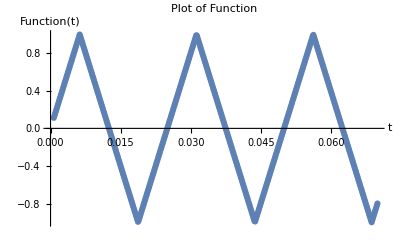

```mathematica
ClearAll["Global`*"]

initialtime = 0.0007;
finaltime = 0.07;
numbintervals = 500;
stepsize = (finaltime-initialtime)/numbintervals;

potFunction[t_]:=TriangleWave[t*40] 

timeinterval = Range[initialtime,finaltime,stepsize];
vector = potFunction[timeinterval];

(*Plot[potFunction[t],{t,0,0.07},PlotRange->All,AxesLabel->{"t","f(t)"},PlotLabel->"Potential"]*)

ListLinePlot[Transpose[{timeinterval, vector}],PlotMarkers->Automatic,AxesLabel->{"t","Function(t)"},PlotLabel->"Plot of Function"]
```

```mathematica
f = OpenWrite["potential.txt",FormatType -> OutputForm]
Write[f,vector]
Close[f]
```

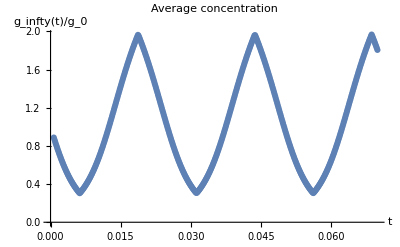

```mathematica
deltag=-3.6;  
length=10*^-6;  
radiustip = 50*^-9;
deltaR = radiusbase - radiustip;
radiusbase = 200*^-9;
radius[x_]:= radiusbase-x*deltaR/length
peclet[V_] := 16.5*V

integrand[V_,x_]:=x*radiustip/(length*radius[x])  - (Exp[peclet[V]*(x/length)*((radiustip^2)/(radiusbase*radius[x]))]-1)/(Exp[peclet[V]*(radiustip/radiusbase)]-1);

ginfinityfun[t_]:=1+(deltag/length)*NIntegrate[integrand[potFunction[t],x],{x,0,length}];
ginfinity = ginfinityfun[ timeinterval];
ListLinePlot[Transpose[{timeinterval,ginfinity}],PlotMarkers->Automatic,AxesLabel->{"t","g_infty(t)/g_0"},PlotLabel->"Average concentration"]
```

```mathematica
ginfinityfun[0.02]
```

3.88

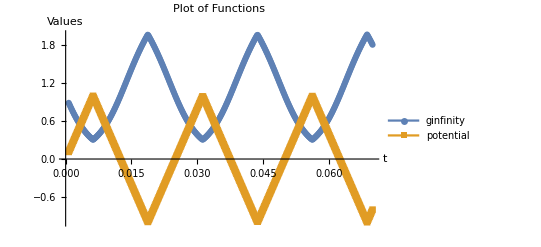

```mathematica
ListLinePlot[{Transpose[{timeinterval,ginfinity}],Transpose[{timeinterval,vector}]},PlotMarkers->Automatic,AxesLabel->{"t","Values"},PlotLabel->"Plot of Functions",PlotLegends->{"ginfinity","potential"}]
```

```mathematica
tau =4.8;
function[t]:=potFunction[t]
sol = DSolve[{g'[t]==(1/tau)*(function[t]-g[t]),g[0]== 1.4},g,{t,initialtime,finaltime}]
Plot[g[t]/. sol,{t,initialtime,finaltime}]
```

NIntegrate::inumr: The integrand -(-1+ⅇ^((0.020625 x TriangleWave[40 t])/(1/5000000+Times[«2»])))/(-1+ⅇ^(4.125 TriangleWave[Times[«2»]]))+x/(200 (1/5000000-(3 x)/200)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumri: The integrand 40 ((4.125 ⅇ^(4.125 TriangleWave[40 t]) (-1+ⅇ^((0.020625 x TriangleWave[Times[«2»]])/Plus[«2»])))/((-1+ⅇ^(4.125 TriangleWave[«1»]))^2)-(0.020625 ⅇ^((0.020625 x «12»[40 t])/(1/5000000+Times[«2»])) x)/((-1+ⅇ^(4.125 TriangleWave[«1»])) (1/5000000-(3 x)/200))) (Piecewise[{{4, Cos[80 π t]>0}, {-4, Cos[80 π t]<0}, {Indeterminate, True}}]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1/100000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{{g→Function[{t},ⅇ^(-0.208333 t) (1.4+-75000. ⅇ^(0.208333 K[1]) (-2.77778×10^-6+1. NIntegrate[integrand[potFunction[K[1]],x],{x,0,length}])K[1]0t)]}}

NIntegrate::inumr: The integrand -(-1+ⅇ^((0.020625 x TriangleWave[40 K[«1»]])/(1/5000000+Times[«2»])))/(-1+ⅇ^(4.125 TriangleWave[Times[«2»]]))+x/(200 (1/5000000-(3 x)/200)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/100000}}.

NIntegrate::inumr: The integrand -(-1+ⅇ^((0.020625 x TriangleWave[40 K[«1»]])/(1/5000000+Times[«2»])))/(-1+ⅇ^(4.125 TriangleWave[Times[«2»]]))+x/(200 (1/5000000-(3 x)/200)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.